```mathematica
<<ProbabilisticBricks`
```

```mathematica
setProblemProperties[5,14,51,27,38.4,0.7];
```

```mathematica
generateContacts[];
```

```mathematica
p=Table[{0,0,517.7,0,0,0},{nelx}];
p[[1]]={0,0,517.7/2,650,0,0};
p[[nelx]]={0,0,517.7/2,0,0,0};
(*p[[5]]={0,0,10,10,0,0};
p[[6]]={0,0,10,-35,0,0};*)
p=Flatten[p];
setBoundaryConditions[p];
```

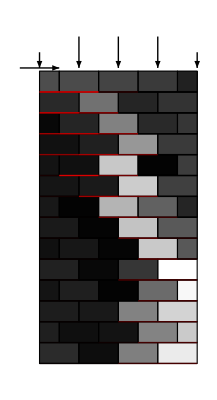

```mathematica
solveProblem[]
```

```mathematica
eqCheck
```

True